This Mathematica notebook refers to the following paper:

I. Palaia, A. Paraschiv, V. Debets, C. Storm, A. Šarić
Durotaxis of passive nanoparticles on elastic membranes
bioRχiv (2021)
https://doi.org/10.1101/2021.04.01.438065

It contains code to compute the free energy of a passive nanoparticle adhering to a fluctuating, bendable membrane. 
First, adhesion energy, bending energy, global stretching, and fluctuation entropy are defined as a function of wrapped area (see Methods section of the paper). 
Then, the constrained free energy resulting from the sum of these terms is minimised, and the equilibrium free energy (see Fig. 3) is output to a file.

Ivan Palaia, 12Jul2021, i.palaia@ucl.ac.uk

## F minimization

Notation:

Σ is wrapped area, in units of σ^2 where σ is the unit of length (e.g. in simulations).
κ is bending rigidity, in units of thermal energy k_B T.
τ is surface tension, in units of k_B T/σ^2.
a is the side of a square whose area equals the area of a small rhombus, defined by the membrane mesh in simulations. In the paper, a = n^(-1/2). It is in units of σ.
ϵ is the adhesion energy per bead, in units of k_B T. In other words, ϵ and a are such that the adhesion energy per surface is ϵ/a^2. See Eq. (6).
R is the radius of the adhered nanoparticle, in units of σ.

δh2Ten is the squared amplitude of fluctuations divided by k_B T, as defined by Eq. (11). It is in units of σ^2/(k_B T).
F is the constrained free energy, in units of k_B T.
Ebend is the bending energy, in units of k_B T.
Eadh is the adhesion energy, in units of k_B T.
Esurf is the energy associated with surface tension, in units of k_B T.
Sm is the entropic term of the free energy -TS, in units of k_B T.

```mathematica
δh2Ten[Σ_,a_,ϵ_,κ_,τ_]:=(-ArcTan[(8 π^2 κ+Σ τ)/(Σ √((248 2^(2/3) ϵ κ)/a^4-τ^2))]+ArcTan[(8 π^2 κ+a^2 τ)/(√(248 2^(2/3) ϵ κ-a^4 τ^2))])/(2 π √((248 2^(2/3) ϵ κ)/a^4-τ^2))
```

```mathematica
F[Σ_,a_,ϵ_,κ_,τ_,R_]:=(2κ)/R^2 Σ - Σ ϵ/a^2+τ Σ^2/(4π R^2)-Σ/a^2  Log[√(δh2Ten[Σ,a,ϵ,κ,τ]/δh2Ten[Σ,a,0,κ,τ])]   
Ebend[Σ_,κ_,R_]:=(2κ)/R^2 Σ ;
Eadh[Σ_,ϵ_,a_]:=- Σ ϵ/a^2;
Esurf[Σ_,τ_,R_]:=+τ Σ^2/(4π R^2);
Sm[Σ_,a_,ϵ_,κ_,τ_]:=-Σ/a^2  Log[√(δh2Ten[Σ,a,ϵ,κ,τ]/δh2Ten[Σ,a,0,κ,τ])]  ;
```

```mathematica
a=1.145;
ϵ=0.7;
τ=0.001;
R=6.17; (* = (10+1)/2*2^(1/6), position of the adhesion energy minimum between nanoparticle and membrane bead *)
```

```mathematica
Manipulate[Plot[{F[Σ,a,ϵ,κ,τ,R,ϵ]/.{κ->10^κexp},(2κ)/R^2 Σ/.{κ->10^κexp} ,- Σ ϵ/a^2,+τ Σ^2/(4π R^2),-Σ/a^2 kT Log[√(δh2Ten[Σ,a,ϵ,κ,τ]/δh2Ten[Σ,a,0,κ,τ])]/.{κ->10^κexp}},{Σ,0,30},PlotLegends->{"Tot","E_bend","E_adh","E_surf","-TS"}, AxesLabel->{"Σ"}],{κexp,-6,3}] 
 (* For a given κ (adjustable through the sliding switch), plot energy contributions as a function of wrapping area Σ*)
```

```mathematica
κList=Catenate[{Table[10^κexp,{κexp,-3,0.5,0.1}],Table[10^κexp,{κexp,0.5,Log10[30],0.04}],Table[10^κexp,{κexp,Log10[30],Log10[40],0.01}],Table[10^κexp,{κexp,Log10[40],2,0.1}]}];   (* List of κ points *)
Fminim=NMinimize[{F[Σ,a,ϵ,#,τ,R],Σ≥0},Σ]  & /@ κList//Chop; (* Minimize constrained free energy F(Σ) *)
ΣbκList=Table[{κList[[i]], Σ/.Fminim[[i,2]]},{i,1,Length[κList]}];   (* Store list of Subscript[Σ, bound] that minimises free energy, for each κ in κList *)
FκList=Table[{κList[[i]], Fminim[[i,1]]},{i,1,Length[κList]}];   (* Store list of equilibrium free energy F (resulting from minimisation with respect to Σ, for each κ in κList *)
```

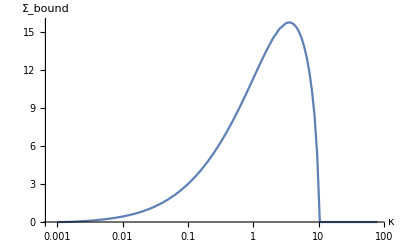

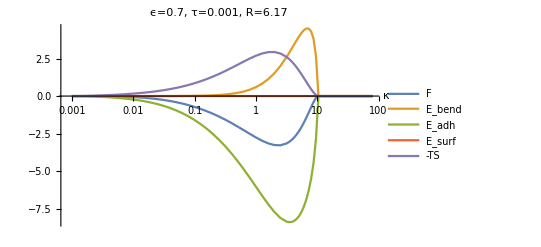

```mathematica
ListLogLinearPlot[ΣbκList,AxesLabel->{"κ","Σ_bound"},Joined->True]   (* Plot of wrapped area Subscript[Σ, bound] vs κ *)
plotFLogLinear=ListLogLinearPlot[{FκList,{#[[1]],Ebend[#[[2]],#[[1]],R]}&/@ΣbκList,{#[[1]],Eadh[#[[2]],ϵ,a]}&/@ΣbκList,{#[[1]],Esurf[#[[2]],τ,R]}&/@ΣbκList,{#[[1]],Sm[#[[2]],a,ϵ,#[[1]],τ]}&/@ΣbκList},AxesLabel->{"κ",""},Joined->True,PlotLegends->{"F","E_bend","E_adh","E_surf","-TS"},PlotLabel->"ϵ="<>ToString[ϵ]<>", τ="<>ToString[τ]<>", R="<>ToString[R], PlotRange->All]    (* Plot of free energy (and its components) vs κ *)
(* 
Same plots in linear scale: 

ListPlot[ΣbκList,AxesLabel->{"κ","Σ_bound"},Joined->True]
plotFLinear=ListPlot[{FκList,{#[[1]],Ebend[#[[2]],#[[1]],R]}&/@ΣbκList,{#[[1]],Eadh[#[[2]],ϵ,a]}&/@ΣbκList,{#[[1]],Esurf[#[[2]],τ,R]}&/@ΣbκList,{#[[1]],Sm[#[[2]],a,ϵ,#[[1]],τ]}&/@ΣbκList},AxesLabel->{"κ",""},Joined->True,PlotLegends->{"F","E_bend","E_adh","E_surf","-TS"},PlotLabel->"ϵ="<>ToString[ϵ]<>", τ="<>ToString[τ]<>", R="<>ToString[R], PlotRange->Full]
*)
```

```mathematica
PrintList=Prepend[
 Table[{
κList[[i]], 
Fminim[[i,1]],
Ebend[ΣbκList[[i,2]],κList[[i]],R],
Eadh[ΣbκList[[i,2]],ϵ,a], 
Esurf[ΣbκList[[i,2]],τ,R], 
Sm[ΣbκList[[i,2]],a,ϵ,κList[[i]],τ]
},{i,1,Length[κList]}]
,
{"#kappa", "F", "E_bending", "E_adhesion", "E_surface", "-TS"}
] // Chop

Export["DurotaxisGit_FreeEnergyContributions_eps"<>ToString[ϵ]<>"_tau"<>ToString[τ]<>"_R"<>ToString[R]<>"_a"<>ToString[a]<>".dat", PrintList]
```

{{#kappa,F,E_bending,E_adhesion,E_surface,-TS},{0.001,1.11712×10^-10,0,-1.22033×10^-9,0,1.33192×10^-9},{0.00125893,0,0,-1.22033×10^-9,0,1.24536×10^-9},{0.00158489,-0.000208178,1.29376×10^-6,-0.00829626,5.04673×10^-10,0.00808678},{0.00199526,-0.00132359,4.26271×10^-6,-0.0217127,3.45678×10^-9,0.0203848},{0.00251189,-0.00364271,9.30409×10^-6,-0.0376445,1.03908×10^-8,0.0339924},{0.00316228,-0.00749347,0.0000176551,-0.0567411,2.3607×10^-8,0.04923},{0.00398107,-0.0132756,0.0000312356,-0.0797402,4.6623×10^-8,0.0664332},{0.00501187,-0.0214689,0.0000530109,-0.107496,8.47288×10^-8,0.0859741},{0.00630957,-0.032641,0.0000875401,-0.141005,1.45786×10^-7,0.108276},{0.00794328,-0.0474539,0.000141799,-0.181427,2.4135×10^-7,0.133831},{0.01,-0.066668,0.000226409,-0.230102,3.88229×10^-7,0.163208},{0.0125893,-0.0911417,0.000357455,-0.288568,6.1058×10^-7,0.197068},{0.0158489,-0.121826,0.000559156,-0.358559,9.42684×10^-7,0.236173},{0.0199526,-0.159753,0.000867758,-0.442004,1.43251×10^-6,0.281382},{0.0251189,-0.206018,0.00133715,-0.541013,2.14615×10^-6,0.333655},{0.0316228,-0.261761,0.0020469,-0.657846,3.17318×10^-6,0.394035},{0.0398107,-0.328138,0.00311372,-0.794889,4.63296×10^-6,0.463632},{0.0501187,-0.4063,0.00470758,-0.954609,6.68185×10^-6,0.543594},{0.0630957,-0.497374,0.00707454,-1.13953,9.52132×10^-6,0.635072},{0.0794328,-0.602437,0.0105685,-1.3522,0.0000134068,0.73918},{0.1,-0.722502,0.0156956,-1.59516,0.0000186575,0.856943},{0.125893,-0.858485,0.0231754,-1.87091,0.0000256657,0.989229},{0.158489,-1.01116,0.0340253,-2.18187,0.0000349064,1.13666},{0.199526,-1.18107,0.0496748,-2.53025,0.0000469433,1.29947},{0.251189,-1.36841,0.0721184,-2.91792,0.0000624298,1.47733},{0.316228,-1.57283,0.104116,-3.34614,0.0000820984,1.66911},{0.398107,-1.79317,0.149449,-3.81522,0.00010673,1.8725},{0.501187,-2.02705,0.213234,-4.32397,0.000137092,2.08355},{0.630957,-2.27035,0.302281,-4.86898,0.000173828,2.29617},{0.794328,-2.51655,0.425463,-5.44363,0.000217282,2.5014},{1.,-2.75586,0.594,-6.0369,0.000267223,2.68677},{1.25893,-2.97425,0.821484,-6.63173,0.000322477,2.83567},{1.58489,-3.15237,1.12331,-7.20326,0.000380455,2.92719},{1.99526,-3.26463,1.51497,-7.71672,0.000436628,2.93668},{2.51189,-3.27886,2.00822,-8.1253,0.000484088,2.83773},{3.16228,-3.15718,2.60367,-8.36783,0.000513418,2.60647},{3.16228,-3.15718,2.60367,-8.36783,0.000513418,2.60647},{3.46737,-3.06141,2.86633,-8.40145,0.000517552,2.47319},{3.80189,-2.93497,3.13868,-8.39023,0.000516171,2.31607},{4.16869,-2.77569,3.41578,-8.32754,0.000508487,2.13557},{4.57088,-2.58184,3.69058,-8.20582,0.000493731,1.93291},{5.01187,-2.35241,3.95318,-8.0163,0.000471187,1.71023},{5.49541,-2.08746,4.1897,-7.74836,0.000440215,1.47076},{6.0256,-1.7886,4.38058,-7.38854,0.000400279,1.21896},{6.60693,-1.45976,4.49761,-6.91846,0.000350966,0.960737},{7.24436,-1.1083,4.49831,-6.31069,0.000292011,0.703788},{7.94328,-0.747061,4.3134,-5.51883,0.000223326,0.458147},{8.70964,-0.398443,3.81185,-4.44798,0.000145068,0.237545},{9.54993,-0.10588,2.64387,-2.81363,0.0000580472,0.0638255},{10.4713,0,1.25733×10^-9,-1.22033×10^-9,0,0},{11.4815,1.59424×10^-10,1.37864×10^-9,-1.22033×10^-9,0,0},{12.5893,2.92334×10^-10,1.51165×10^-9,-1.22033×10^-9,0,0},{13.8038,4.38085×10^-10,1.65749×10^-9,-1.22033×10^-9,0,0},{15.1356,5.97915×10^-10,1.8174×10^-9,-1.22033×10^-9,0,0},{16.5959,7.7318×10^-10,1.99274×10^-9,-1.22033×10^-9,0,0},{18.197,9.65367×10^-10,2.18499×10^-9,-1.22033×10^-9,0,0},{19.9526,1.17611×10^-9,2.3958×10^-9,-1.22033×10^-9,0,0},{21.8776,1.4072×10^-9,2.62694×10^-9,-1.22033×10^-9,0,0},{23.9883,1.66059×10^-9,2.88038×10^-9,-1.22033×10^-9,0,0},{26.3027,1.93843×10^-9,3.15828×10^-9,-1.22033×10^-9,0,0},{28.8403,2.24309×10^-9,3.46298×10^-9,-1.22033×10^-9,0,0},{30.,2.38233×10^-9,3.60223×10^-9,-1.22033×10^-9,0,0},{30.6988,2.46622×10^-9,3.68613×10^-9,-1.22033×10^-9,0,0},{31.4139,2.55207×10^-9,3.772×10^-9,-1.22033×10^-9,0,0},{32.1456,2.63993×10^-9,3.85986×10^-9,-1.22033×10^-9,0,0},{32.8943,2.72982×10^-9,3.94976×10^-9,-1.22033×10^-9,0,0},{33.6606,2.82182×10^-9,4.04177×10^-9,-1.22033×10^-9,0,0},{34.4446,2.91595×10^-9,4.13591×10^-9,-1.22033×10^-9,0,0},{35.2469,3.01228×10^-9,4.23225×10^-9,-1.22033×10^-9,0,0},{36.0679,3.11086×10^-9,4.33083×10^-9,-1.22033×10^-9,0,0},{36.9081,3.21173×10^-9,4.43171×10^-9,-1.22033×10^-9,0,0},{37.7678,3.31495×10^-9,4.53494×10^-9,-1.22033×10^-9,0,0},{38.6475,3.42057×10^-9,4.64057×10^-9,-1.22033×10^-9,0,0},{39.5477,3.52866×10^-9,4.74866×10^-9,-1.22033×10^-9,0,0},{40.,3.58296×10^-9,4.80297×10^-9,-1.22033×10^-9,0,0},{50.357,4.82651×10^-9,6.04658×10^-9,-1.22033×10^-9,0,0},{63.3957,6.39207×10^-9,7.6122×10^-9,-1.22033×10^-9,0,0},{79.8105,8.36302×10^-9,9.58319×10^-9,-1.22033×10^-9,0,0}}

DurotaxisGit_FreeEnergyContributions_eps0.7_tau0.001_R6.17_a1.145.dat